## LC Matching Network

```mathematica
Subscript[Z, c]=50; Subscript[Z, l]=100;α=Subscript[Z, l]/Subscript[Z, c];Subscript[Y, l]=1/Subscript[Z, l];Subscript[Y, c]=1/Subscript[Z, c];
(*x will represent Subscript[βl, l] and y will represent Subscript[βl, s]*)
```

```mathematica
Subscript[X, b]=Sqrt[(α^2 Subscript[Z, c]^2)/(α-1)]
```

100

```mathematica
Subscript[X, a]=-Subscript[Z, c]Sqrt[α-1]
```

-50

## Single Open Stub

```mathematica
RealEq[x_,y_]:=Re[(Subscript[Y, l]+I Subscript[Y, c] Tan[x])/(Subscript[Y, c]+I Subscript[Y, l] Tan[x])+I Tan[y]]
ImagEq[x_,y_]:=Im[(Subscript[Y, l]+I Subscript[Y, c] Tan[x])/(Subscript[Y, c]+I Subscript[Y, l] Tan[x])+I Tan[y]]
```

```mathematica
FindRoot[{RealEq[x,y]==1,ImagEq[x,y]==0},{x,1},{y,2.5}]
Plot3D[RealEq[x,y],{x,0,2π},{y,0,2π},AxesLabel-> {Subscript[β, Subscript[l, l]],Subscript[β, Subscript[l, s]],"Real Part"}]
Plot3D[ImagEq[x,y],{x,0,2π},{y,0,2π},AxesLabel-> {Subscript[β, Subscript[l, l]],Subscript[β, Subscript[l, s]],"Imaginary Part"}]
```

{x→0.955317,y→2.52611}

-Graphics3D-

-Graphics3D-

```mathematica
d = Pi/4;
StubAdmittance[l_]:=I Subscript[Y, c] Tan[l];
LoadAdmittance[length_]:=Subscript[Y, c](Subscript[Y, l]+I Subscript[Y, c] Tan[length])/(Subscript[Y, c]+I Subscript[Y, l] Tan[length]);
Y1[t_,l_]:= StubAdmittance[t]+LoadAdmittance[l];
Y2[t_,l_]:=Subscript[Y, c](Y1[t,l]+I Subscript[Y, c] Tan[l])/(Subscript[Y, c]+I Y1 [t,l]Tan[l]);
```

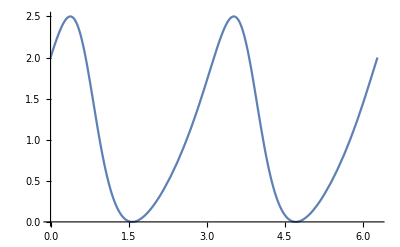

-Graphics3D-

{0.943655,1.14837}

```mathematica
Plot[Re[Y2[x,d]/Subscript[Y, c]],{x,0,2 Pi}]
Plot3D[Subscript[Z, c](Im[Y2[x,d]]+Im[StubAdmittance[y]]),{x,0,2 Pi},{y,0,2 Pi}]
{Subscript[β, Subscript[l, s]],Subscript[β, Subscript[l, l]]}={x,y}/.FindRoot[{Re[Y2[x,d]]==Subscript[Y, c],Im[Y2[x,d]]==-Im[StubAdmittance[y]]},{x,.5},{y,.1}]
```

```mathematica
{Subscript[β, Subscript[l, s]],Subscript[β, Subscript[l, l]]}*180/Pi
```

{54.0675,65.7966}